# Sister Meccanici e Modelli

# JACOPO DALLAFIOR 218931, jacopo.dallafior@unitn.it

## Dinamica del trabucco

Si consideri il trabucco mostrato in figura. Le principali caratteristiche geometriche ed inerziali sono annotate. Il baricentro G1 sta a metà della trave (1). I momenti di inerzia baricentrici sono I1 =1/12 m1 L^2 e  I2 = 1/12 m2 L2^2.

Il trabucco è un sistema ibrido, nel senso che ha due configurazioni distinte: 1) a sinistra, quando il proiettile m3 è appoggiato al suolo il sistema ha 2 gradi di libertà. In questa situazione m3 è soggetto alla reazione vincolare del suolo. Si suppone che ci sia attrito con il suolo e che sia fc il coefficiente di attrito cinetico; 2) a destra, quando il proiettile si alza da suolo, il trabucco ha 3 gradi di libertà, ma mancano le forze normale e di attrito del suolo.

Modellare la corda CD come un’asta senza massa (salvo verificare più tardi che non vada mai in compressione).

-Graphics-

Si richiede:

a) Scrivere le equazioni del moto nelle due situazioni 1 e 2 sopra dette.

b) Nel caso 1, determinare le reazioni vincolari, compresa la forza normale del suolo sulla massa m3, ed esplicitare due equazioni per i due gradi di libertà (osservazione: in contatto con il suolo, l’angolo θ3 dell’asta CD è determinato dalle equazioni di chiusura ed è quindi un cedente).

c) Determinare le condizioni iniziali per le due equazioni del moto, corrispondenti alla configurzione a sinistra.

d) Assumendo i seguenti parametri h =10; L=20; L1 =2;  m1 = 5; L2=2;m2 = 10000; L3=15; m3 =200; g=9.8; fc =0.2;  calcolare le accelerazioni e le forze iniziali.

e) Integrare le equazioni del moto (NDSolve) con le condizioni iniziali precedenti. Terninare l'integrazione nel momento in cui m3 si stacca dal suolo (suggerimento: utilizzare l'opzione WhenEvent per bloccare l'integrazione dopo aver formulato la condizione corrispondente al distacco, e cioè che la reazione del suolo sia diventata zero). Realizzare un'animazione del movimento ottenuto.

f) Nel caso 2, ricavare le espressioni per le reazioni vincolari (ora manca la forza del suolo) ed esplicitare le 3 equazioni differenziali per i 3 gradi di libertà.

g ) Determinare le condizioni iniziali al momento del distacco (suggerimento ricavarle dalle condizioni finali del punto precedente) e integrare le equazioni. Terminare l’integrazione nel momento in cui la corda diventa lasca (l’asta CD va in compressione). Rappresentare graficamente la tensione della corda. Realizzare una animazione anche per la fase 2.

h) Calcolare la gittata che si avrebbe rilasciando la massa m3  ad un tempo t generico (suggerimento usare le formule della Fisica 1) e determinare l’istante in cui la gittata è massima e il valore di gittata ottenuta (FindMaximum).

i) Provare con diversi valori della massa m3 a massimizzare la gittata.

## a) Scrivere le equazioni del moto nelle due situazioni 1 e 2 sopra dette.

#### POSIZIONE BARICENTRI

```mathematica
(*trovo le coordinate dei vari baricentri*)
XG1=0+(L/2-L1) Cos[θ1[t]];
YG1=h+(L/2-L1) Sin[θ1[t]];
XG2=0-L1 Cos[θ1[t]]+L2 Cos[θ2[t]];
YG2=h-L1 Sin[θ1[t]]+L2 Sin[θ2[t]];
XG3=0+(L-L1) Cos[θ1[t]]+L3 Cos[θ3[t]];
YG3=h+(L-L1) Sin[θ1[t]]+L3 Sin[θ3[t]];
OA={0,h};
OB=OA+L1{-Cos[θ1[t]],-Sin[θ1[t]]};
OC=OA+(L-L1) {Cos[θ1[t]],Sin[θ1[t]]};
OD=OC+L3 {Cos[θ3[t]],Sin[θ3[t]]};
OG2=OB+L2 {Cos[θ2[t]],Sin[θ2[t]]};
(*Ora ricavo le equazioni di newtoon-eulero*)
```

#### MOMENTI

```mathematica
Mm1A = ({((L/2-L1) Cos[θ1[t]]),((L/2-L1) Sin[θ1[t]]),0}×{0,m1*g,0})[[3]];
MRBA= ({((L1) Cos[θ1[t]]),((L1) Sin[θ1[t]]),0}×{RBx,RBy,0})[[3]];
MRCA= ({((L-L1) Cos[θ1[t]]),((L-L1)Sin[θ1[t]]),0}×{RC Cos[θ3[t]],RC Sin[θ3[t]],0})[[3]];
(*Trovo i 3 momenti rispetto al punto A e quello rispetto al baricentro G2*)
MRBG2= ({((L2) Cos[θ2[t]]),((L2) Sin[θ2[t]]),0}×{RBx,RBy,0})[[3]];
```

#### EQUAZIONI N-E DEI COPRI

N-E COPRO 1

```mathematica
ENx1= m1 D[D[XG1, t], t]==RAx+RC Cos[θ3[t]]-RBx;
ENy1= m1 D[D[YG1, t], t]==RAy+RC Sin[θ3[t]]-RBy-m1*g;
EE1=I1a D[D[θ1[t], t], t]==MRBA-Mm1A+MRCA;
```

N-E CORPO 2

```mathematica
ENx2= m2 D[D[XG2, t], t]==RBx;
ENy2= m2 D[D[YG2, t], t]==RBy-m2*g;
EE2=I2 D[D[θ2[t], t], t]==-MRBG2;
```

N-E CORPO 3

```mathematica
ENx3= m3 D[D[XG3, t], t]==-RC Cos[θ3[t]]-N3 *fc;
ENy3= m3 D[D[YG3, t], t]==-RC Sin[θ3[t]]-m3*g+N3;
EE3= I3 D[D[θ3[t], t], t]==0 ;(*COPRO PUNTIFORME I3=0, nella seconda fase si avrà la forza N3=0*)
```

NELLA SECONDA FASE SI AVRA’  N3=0

#### DISEGNO REAZIONI VINCOLARI

-Graphics-

```mathematica
θ1[t_]:=q1[t];
θ2[t_]:=q2[t];
```

## b) Nel caso 1, determinare le reazioni vincolari, compresa la forza normale del suolo sulla massa m3, ed esplicitare due equazioni per i due gradi di libertà (osservazione: in contatto con il suolo, l’angolo θ3 dell’asta CD è determinato dalle equazioni di chiusura ed è quindi un cedente).

#### REAZIONI VINCOLARI

```mathematica
(*Determino le reazioni vincolari ricvandole dalle equazioni di Newton*)
```

```mathematica
REV=Simplify@Solve[{ENx1,ENy1,ENx2,ENy2,ENx3,ENy3},{RAx,RAy,RBx,RBy,RC,N3}]
```

#### EQUAZIONI PER I DUE GdL

```mathematica
EQ1EQ2=Simplify[{EE1,EE2}/.REV]
```

## c) Determinare le condizioni iniziali per le due equazioni del moto, corrispondenti alla configurzione a sinistra.

```mathematica
CI={q2[0]==3/2 π, q2'[0]==0,q1[0]==-ArcSin[h/(L-L1)],q1'[0]==0};
```

## d) Assumendo i seguenti parametri h =10; L=20; L1 =2; m1 = 5; L2=2;m2 = 10000; L3=15; m3 =200; g=9.8; fc =0.2; calcolare le accelerazioni e le forze iniziali.

#### VINCOLO DI CONTATTO

```mathematica
(*Trovo il vincolo di contatto tramite equazione di chiusura*)
EQUAZIONEY= -L3 Sin[θ3[t]]-(L-L1) Sin[θ1[t]]-h==0;
First@Simplify@Solve[{EQUAZIONEY},{θ3[t]}]/.C[1]->0
```

```mathematica
θ3[t_]=π+ArcSin[(h+(L-L1) Sin[θ1[t]])/L3];
```

#### PARAMETRI

```mathematica
(*Inserisco i parametri forniti facendo attenzione a adeguare il momento d'inerzia del copro 1 rispetto al polo A*)
h=10;L=20;L1=2;m1=5;L2=2;m2=10000;L3=15;m3=200;g=9.8;fc=0.2;I1a=1/12 m1 L^2 +m1*(L/2-L1)^2;
I2=1/12 m2 L2^2;
```

#### EQUAZIONI PER I DUE GdL con i parametri

```mathematica
eq1eq2=Simplify[EQ1EQ2];
```

#### EQUAZIONI DEL MOTO CON C.I. E I PARAMETRI

```mathematica
So0={ENx1,ENy1,ENx2,ENy2,ENx3,ENy3,EE1,EE2}/.t->0/.{q2[0]->3/2 π, q2'[0]->0,q1[0]->-ArcSin[h/(L-L1)],q1'[0]->0}
```

#### ACCELERAZIONI E FORZE INIZIALI

```mathematica
Solve[So0,{RAx,RAy,RBx,RBy,RC,N3,q1''[0],q2''[0]}]
```

## e) Integrare le equazioni del moto (NDSolve) con le condizioni iniziali precedenti. Terninare l’integrazione nel momento in cui m3 si stacca dal suolo (suggerimento: utilizzare l’opzione WhenEvent per bloccare l’integrazione dopo aver formulato la condizione corrispondente al distacco, e cioè che la reazione del suolo sia diventata zero). Realizzare un’animazione del movimento ottenuto.

#### INTEGRAZIONE EQUAZIONI DEL MOTO

```mathematica
(*Integro le equazioni del moto con le condizioni iniziali, tramite il WhenEvent blocco l'integrazione quando N3=0*)
```

```mathematica
Tnull=WhenEvent[Evaluate[N3==0/.REV],"StopIntegration"];
sis=Union[{eq1eq2,CI,Tnull}];
soluz1=First@NDSolve[sis,{q1,q2},{t,0,15},Method->{"EquationSimplification"->"Residual"}]
```

```mathematica
EV1=Evaluate[{OG2,OB,OA,OC,OD}/.soluz1];
```

```mathematica
(*con tdist->tempo del distacco*)
```

```mathematica
tdist=(q1/.soluz1)["Domain"][[1,2]]
```

#### ANIMAZIONE PRIMA PARTE

```mathematica
Animate[ListLinePlot[Block[{t=τ},EV1],PlotRange->Automatic],{τ,0,tdist}]
```

## f) Nel caso 2, ricavare le espressioni per le reazioni vincolari (ora manca la forza del suolo) ed esplicitare le 3 equazioni differenziali per i 3 gradi di libertà.

#### TROVO LE CONDIZIONI FINALI RICAVANDOLE DAL PUNTO PRECEDENTE

```mathematica
CF={q1[tdist],q1'[tdist],q2[tdist],q2'[tdist],θ3[tdist],θ3'[tdist]}/.soluz1
```

#### NUOVO GdL

```mathematica
(*Ora devo rimovere la forza del suolo e avrò un nuovo GdL*)
Clear[h,L,L1,L2,m1,m2,m3,I1a,I2,L3,g,fc,θ3]
N3=0;
θ3[t_]:=q3[t];
```

#### REAZIONI VINCOLARI

```mathematica
REV2=Simplify@Solve[{ENx1,ENy1,ENx2,ENy2,ENy3},{RAx,RAy,RBx,RBy,RC}]
```

#### EQUAZIONI PER I 3 GdL

```mathematica
EQ1EQ2EQ3=Simplify[{EE1,EE2,ENx3}/.REV2]
```

## g ) Determinare le condizioni iniziali al momento del distacco (suggerimento ricavarle dalle condizioni finali del punto precedente) e integrare le equazioni. Terminare l’integrazione nel momento in cui la corda diventa lasca (l’asta CD va in compressione). Rappresentare graficamente la tensione della corda. Realizzare una animazione anche per la fase 2.

#### CONDIZIONI INIZIALI AL MOMENTO DEL DISTACCO

```mathematica
(*Condizioni iniziali al momento del distacco sono quelle finali del punto precedente 
CF={q1[tdist],q1'[tdist],q2[tdist],q2'[tdist],q3[tdist],q3'[tdist]}/.soluz1*)
CF1={q2[tdist]==4.81205, q2'[tdist]==0.34655,q1[tdist]==-0.340754,q1'[tdist]==1.20966,θ3[tdist]==3.41045,θ3'[tdist]==1.41915};
```

#### PARAMETRI

```mathematica
h=10;L=20;L1=2;m1=5;L2=2;m2=10000;L3=15;m3=200;g=9.8;fc=0.2;I1a=1/12 m1 L^2 +m1*(L/2-L1)^2;
 I2=1/12 m2 L2^2;
```

#### EQUAZIONI PER I TRE GdL con i parametri

```mathematica
eq1eq2eq3=Simplify[EQ1EQ2EQ3];
```

#### INTEGRAZIONE EQUAZIONI DEL MOTO CON ASTA CHE VA IN COMPRESSIONE

```mathematica
Tnull1=WhenEvent[Evaluate[RC==0/.REV2],"StopIntegration"];
sis2=Union[{eq1eq2eq3,CF1,Tnull1}];
soluz2=First@NDSolve[sis2,{q1,q2,q3},{t,tdist,∞},Method->{"EquationSimplification"->"Residual"}]
```

```mathematica
tdist2=(q1/.soluz2)["Domain"][[1,2]]
```

#### SI RAPPRESENTA ORA LA TENSIONE DELLA CORDA

```mathematica
Plot[Evaluate[Simplify@Evaluate[{RC}/.REV2]/.soluz2],{t,tdist,tdist2},PlotRange->All]
```

#### ANIMAZIONE SECONDA PARTE

```mathematica
EV2=Evaluate[{OG2,OB,OA,OC,OD}/.soluz2];
```

```mathematica
Animate[ListLinePlot[Block[{t=R},EV2],PlotRange->{{-5,40},{-5,40}},AspectRatio->1],{R,tdist,tdist2}]
```

## h) Calcolare la gittata che si avrebbe rilasciando la massa m3 ad un tempo t generico (suggerimento usare le formule della Fisica 1) e determinare l’istante in cui la gittata è massima e il valore di gittata ottenuta (FindMaximum).

#### GITTATA E VALORE MASSIMO

```mathematica
(*Calcolo la gittata X e il tempo di volo Tv*)
Tv=2(D[OD[[2]], t])/g;
X=(D[OD[[1]], t])*Tv;
valmax=FindMaximum[X/.soluz2,{t,tdist,tdist2}]
```

```mathematica
valmin=FindMinimum[X/.soluz2,{t,1.4563,tdist2}]
```

Per come è pensato il trabucco vado a considerare la gittata negativa, poichè quella è nella direzione desiderata di lancio

#### GRAFICO GITTATA

```mathematica
Plot[Evaluate[X/.soluz2,{t,tdist,tdist2}],PlotRange->All]
```

## i) Provare con diversi valori della massa m3 a massimizzare la gittata.

TROVO LE GITTATE MASSIME IN ENTRAMBI LE DIREZIONI (quella che mi interessa è la negativa, quella evidenziata, per come è pensato il trabucco)

Noterò che: piu la massa del corpo 3 è leggera, più la gittata aumenta, si ha una correlazione di proporzionalità inversa.

Noterò che: all’aumentare della massa del corpo 3 aumenta anche il tempo di volo, si ha una correlazione di proporzionalità diretta.

```mathematica
(*Eseguo l'HW2 per piu casi andando a variare la massa 3 nei dati*)
```

MASSA A 50kg

{515.041,{t→0.830655}}

{-649.782,{t→1.11997}}

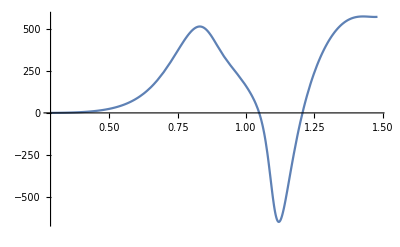

MASSA A 150 Kg

{270.007,{t→1.03872}}

{-192.55,{t→1.48125}}

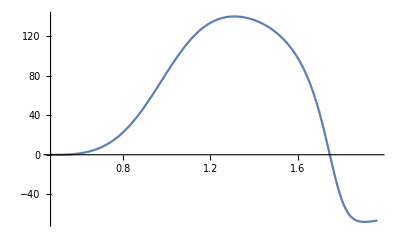

MASSA A 100 Kg

{360.83,{t→0.937291}}

{-312.558,{t→1.31281}}

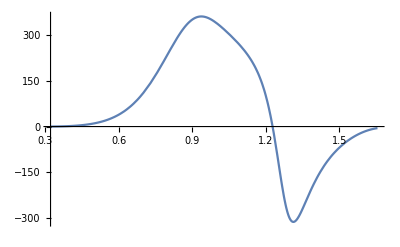

MASSA A 250 Kg

{-93.3643,{t→1.77942}}

{169.886,{t→1.2246}}

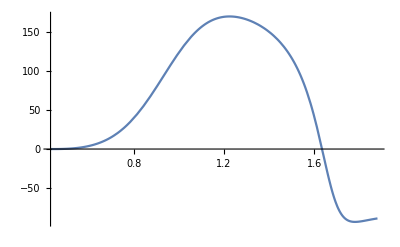

MASSA A 300Kg

{139.779,{t→1.31029}}

{-67.88,{t→1.90519}}

-Graphics-